```mathematica
CDF[NormalDistribution[]]
```

Function[x,1/2 Erfc[-x/(√2)]]

```mathematica
CDF[NormalDistribution[]][x]
```

1/2 Erfc[-x/(√2)]

```mathematica
CDF[NormalDistribution[]][x]//TraditionalForm
```

1/2 erfc(-x/(√2))

```mathematica
CDF[BinomialDistribution[b,c]][x]//TraditionalForm
```

Piecewise[{{1-cb-Floor[x]Floor[x]+1, 0≤x<b}, {1, x≥b}}]

```mathematica
CDF[BetaBinomialDistribution[b,c,d]][x]//TraditionalForm
```

Piecewise[{{1-(c+d-Floor[x]-1b+Floor[x]+1 _3 F_2(1,b+Floor[x]+1,-d+Floor[x]+1;Floor[x]+2,-c-d+Floor[x]+2;1))/((d+1) bc d-Floor[x]Floor[x]+2), 0≤x<d}, {1, x≥d}}]

```mathematica
PDF[BinomialDistribution[2,0.5]]
```

Function[x,Piecewise[{{0.25 Binomial[2,x], 0≤x≤2}, {0, True}}],Listable]

```mathematica
CDF[BinomialDistribution[2,0.5]][1.5]
```

0.75

```mathematica
CDF[BinomialDistribution[2,0.5]][0]
```

0.25

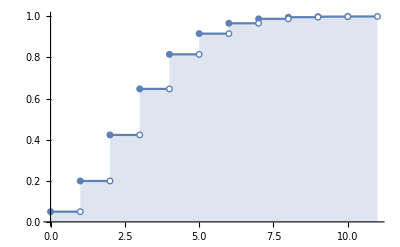

```mathematica
DiscretePlot[CDF[PoissonDistribution[3],k],{k,0,10},ExtentSize->Right,ExtentMarkers->{"Filled","Empty"}]
```

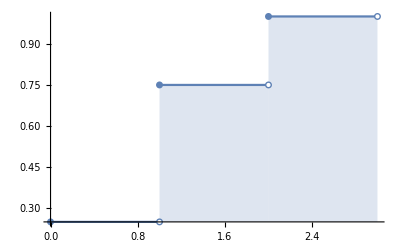

```mathematica
DiscretePlot[CDF[BinomialDistribution[2,0.5],k],{k,0,2},ExtentSize->Right,ExtentMarkers->{"Filled","Empty"}]
```

```mathematica
FunctionMonotonicity[CDF[BinomialDistribution[2,0.5]][x],x]
```

1

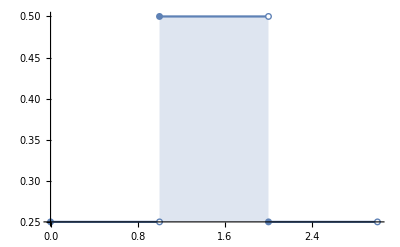

```mathematica
DiscretePlot[PDF[BinomialDistribution[2,0.5],k],{k,0,2},ExtentSize->Right,ExtentMarkers->{"Filled","Empty"}]
```

```mathematica
𝒟=BinomialDistribution[2,0.5];
```

```mathematica
Mean[𝒟]
```

1.

```mathematica
ℰ=EmpiricalDistribution[{1/4,1/2,1/4}->{0,1,2}]
```

DataDistribution[…]

```mathematica
Mean[ℰ]
```

1

```mathematica
Variance[ℰ]
```

1/2

```mathematica
StandardDeviation[ℰ]
```

1/(√2)

```mathematica
Names["*entropy*",IgnoreCase->True]
```

{CrossEntropyLossLayer,Entropy,EntropyFilter}

```mathematica
Information/@Names["*entropy*",IgnoreCase->True]
```

{,,}

flip a coin 2 times

WolframAlphaQueryResults

```mathematica
WebSessionObject[]
```

WebSessionObject[]

```mathematica
StartWebSession["Chrome"]
```

WebSessionObject[…]

```mathematica
randomViolations=EmpiricalDistribution[{0.6,0.25,0.10,0.05}->{0,1,2,3}]
```

DataDistribution[…]

```mathematica
Total[{0.6,0.25,0.10,0.05}]
```

1.

```mathematica
Expectation[y,y\[Distributed]randomViolations]
```

0.6

```mathematica
Mean[randomViolations]
```

0.6

```mathematica
Variance[randomViolations]
```

0.74

```mathematica
Expectation[100 y^2,y\[Distributed]randomViolations]
```

110.

```mathematica
Expectation[y^2,y\[Distributed]randomViolations]
```

1.1

```mathematica
freezerVolumes=EmpiricalDistribution[{0.2,0.5,0.3}->{13.5,15.9,19.1}]
```

DataDistribution[…]

```mathematica
Expectation[x,x\[Distributed]freezerVolumes]
```

16.38

```mathematica
Expectation[x^2,x\[Distributed]freezerVolumes]
```

272.298

```mathematica
Variance[freezerVolumes]
```

3.9936

```mathematica
Expectation[25x-8.5,x\[Distributed]freezerVolumes]
```

401.

```mathematica
TransformedDistribution[25x-8.5,x\[Distributed]freezerVolumes]
```

DataDistribution[…]

```mathematica
Variance[TransformedDistribution[25x-8.5,x\[Distributed]freezerVolumes]]
```

2496.

```mathematica
Mean[TransformedDistribution[25x-8.5,x\[Distributed]freezerVolumes]]
```

401.

```mathematica
Mean[TransformedDistribution[x-0.01 x^2,x\[Distributed]freezerVolumes]]
```

13.657

```mathematica
EmpiricalDistribution[{1/15,2/15,3/15,4/15,3/15,2/15}->Range[6]]
```

DataDistribution[…]

```mathematica
Limit[BinomialDistribution[n,8],n->∞]
```

lim_(n→∞) BinomialDistribution[n,8]

```mathematica
Names["*Binomial*"]
```

{BetaBinomialDistribution,BetaNegativeBinomialDistribution,Binomial,BinomialDistribution,BinomialPointProcess,BinomialProcess,NegativeBinomialDistribution,QBinomial}

```mathematica
Information/@Names["*Binomial*"]
```

{,,,,,,,}

```mathematica
data=RandomVariate[BinomialDistribution[10000,0.3],10000];
```

```mathematica
DistributionFitTest[data,BinomialDistribution[1,0.3]]
```

0.

```mathematica
ℋ=DistributionFitTest[data,BinomialDistribution[1,0.3],"HypothesisTestData"];
```

```mathematica
ℋ["TestDataTable",All]
```

| Statistic | P-Value
Pearson χ^2 | 10000. | 0.

```mathematica
FindDistributionParameters[data,BinomialDistribution[n,p]]
```

{n→9887,p→0.303463}

```mathematica
myBinomialFunction[n_,p_]:=(x↦Binomial[n,x] p^x(1-p)^(n-x))/@Range[0,n]
```

```mathematica
myBinomialFunction[5,0.5]
```

{0.03125,0.15625,0.3125,0.3125,0.15625,0.03125}

```mathematica
Rationalize/@myBinomialFunction[5,0.5]
```

{1/32,5/32,5/16,5/16,5/32,1/32}

```mathematica
Total[{1/32,5/32,5/16,5/16,5/32,1/32}]
```

1

```mathematica
Names["*Bernoulli*"]
```

{BernoulliB,BernoulliDistribution,BernoulliGraphDistribution,BernoulliProcess,NBernoulliB}

```mathematica
Information/@Names["*Bernoulli*"]
```

{,,,,}

```mathematica
ResourceSearch["*Distribution*"]
```

```mathematica
Names["*Wishart*"]
```

{InverseWishartMatrixDistribution,WishartMatrixDistribution}

```mathematica
Information/@Names["*Wishart*"]
```

{,}

```mathematica
Binomial[4,2]
```

6

```mathematica
Permutations[{"S","S","F","F"}]
```

{{S,S,F,F},{S,F,S,F},{S,F,F,S},{F,S,S,F},{F,S,F,S},{F,F,S,S}}

```mathematica
ResourceObject["Prussian Horse Kick Data"]
```

ResourceObject[…]

```mathematica
ResourceData["Prussian Horse Kick Data"]
```

```mathematica
Probability[x>=1,x\[Distributed]BinomialDistribution[10,0.5]]
```

0.999023

```mathematica
SurvivalFunction[BinomialDistribution[10,0.5],x]
```

Piecewise[{{BetaRegularized[0.5,1+Floor[x],10-Floor[x]], 0≤x<10}, {1, x<0}, {0, True}}]

```mathematica
SurvivalFunction[BinomialDistribution[10,0.5],1]
```

0.989258

```mathematica
SurvivalFunction[NegativeBinomialDistribution[10,0.5],2]
```

0.980713

```mathematica
Probability[x>=1,x\[Distributed]BinomialDistribution[10,0.5]]
```

0.999023

```mathematica
SurvivalFunction[NegativeBinomialDistribution[10,0.5],0]
```

0.999023

```mathematica
Probability[x>=2,x\[Distributed]BinomialDistribution[10,0.5]]
```

0.989258

```mathematica
SurvivalFunction[NegativeBinomialDistribution[10,0.5],1]
```

0.994141

```mathematica
circuitBoardDefective=BinomialDistribution[25,0.05];
```

```mathematica
Probability[x<=2,x\[Distributed]circuitBoardDefective]
```

0.872894

```mathematica
Probability[x>=5,x\[Distributed]circuitBoardDefective]
```

0.00716495

```mathematica
Probability[1<=x<=4,x\[Distributed]circuitBoardDefective]
```

0.715445

```mathematica
Probability[x==0,x\[Distributed]circuitBoardDefective]
```

0.27739

```mathematica
Mean[circuitBoardDefective]
```

1.25

```mathematica
Expectation[x,x\[Distributed]circuitBoardDefective]
```

1.25

```mathematica
StandardDeviation[circuitBoardDefective]
```

1.08972

```mathematica
√(25 0.05 (1-0.05))
```

1.08972

```mathematica
NProbability[x<=2,x\[Distributed]circuitBoardDefective,WorkingPrecision->30]
```

0.872893504339067205499702595262

```mathematica
Binomial[25,0] 0.05^0(0.95)^(25-0)+Binomial[25,1](0.05)^1(0.95)^(25-1)+Binomial[25,2](0.05)^2
```

```mathematica
(0.95)^(25-2)
```

0.307357

```mathematica
myBinomialFunction[25,0.05]
```

{0.27739,0.364986,0.230518,0.0930159,0.0269257,0.00595199,0.00104421,0.000149173,0.0000176652,1.75619×10^-6,1.47889×10^-7,1.06141×10^-8,6.51741×10^-10,3.43022×10^-11,1.54747×10^-12,5.97268×10^-14,1.9647×10^-15,5.47439×10^-17,1.28056×10^-18,2.48308×10^-20,3.92065×10^-22,4.91309×10^-24,4.70152×10^-26,3.22759×10^-28,1.41561×10^-30,2.98023×10^-33}

```mathematica
Take[myBinomialFunction[25,0.05],3]
```

{0.27739,0.364986,0.230518}

```mathematica
Total[Take[myBinomialFunction[25,0.05],3]]
```

0.872894

```mathematica
0.95^25
```

0.27739

```mathematica
SliceDistribution[BinomialProcess[λ],t]
```

BinomialDistribution[t,λ]

```mathematica
NProbability[x>=24,x\[Distributed]BinomialDistribution[50,0.5]]
```

0.664094

```mathematica
NProbability[x>=24,x\[Distributed]BinomialDistribution[50,0.5],WorkingPrecision->100]
```

0.66409448311731722469630767591297626495361328125

```mathematica
Expectation[x^2-5,x\[Distributed]BinomialDistribution[50,0.5]]
```

632.5

```mathematica
NExpectation[x^2-5,x\[Distributed]BinomialDistribution[50,0.5],WorkingPrecision->40]
```

632.4999999999999920063942226988729089499

```mathematica
$TutorialDirectory
```

C:\Users\peter\Documents\GitHub\recreational-mathematics\RecreationalMathematics\Documentation\English\Tutorials\

```mathematica
SystemOpen["C:\\Users\\peter\\Documents\\GitHub\\recreational-mathematics\\RecreationalMathematics\\Documentation\\English\\Tutorials\\"]
```

```mathematica
$UserBaseDirectory
```

C:\Users\peter\AppData\Roaming\Mathematica

```mathematica
SystemOpen["C:\\Users\\peter\\AppData\\Roaming\\Mathematica"]
```

```mathematica
$BaseDirectory
```

C:\ProgramData\Mathematica

```mathematica
SystemOpen["C:\\ProgramData\\Mathematica"]
```